{{17.0214,0.298186},{17.8545,0.290249},{19.1811,0.274376},{20.4836,0.260771},{22.945,0.236961},{24.7975,0.22449},{26.7996,0.212018},{29.1368,0.198413},{31.8677,0.185941},{35.4846,0.171202},{39.0428,0.159864},{44.7919,0.145125},{50.7774,0.133787},{60.0203,0.120181},{71.3706,0.10771},{87.9638,0.0952381},{109.064,0.0827664},{140.16,0.0725624},{174.822,0.0646259},{224.666,0.0578231},{315.782,0.0487528},{430.792,0.0430839},{707.224,0.0362812},{1030.31,0.031746},{1492.07,0.0294785}}

```mathematica
model=√((a0/(√x))^2+(b0/x)^2+c0^2);
```

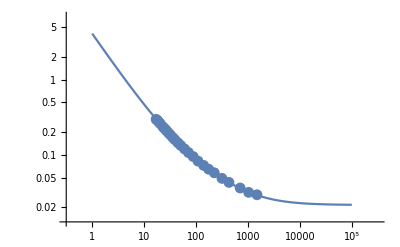

a | 0.749233
b | 4.07086
c | 0.0215534

```mathematica
data=Import["/Users/kazuki/Projects/Atom-work/object-validation/jets/make_yaml/eta_lt_08.dat"];
fit=FindFit[data,model,{a0,b0,c0},x];
modelf=Function[{x},Evaluate[model/.fit]];
Fa=LogLogPlot[modelf[x],{x,1,100000},Epilog->Map[Point,data]];
Fb=ListLogLogPlot[data];
Show[Fa,Fb]
{a,b,c}={a0,b0,c0}/.fit;
{{"a",a},{"b",b},{"c",c}}//TableForm
```

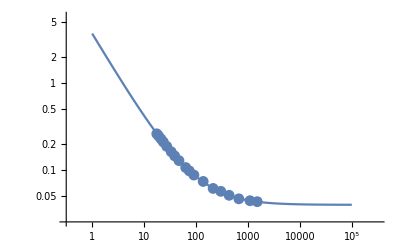

a | 0.640893
b | -3.66528
c | 0.0395407

```mathematica
data=Import["/Users/kazuki/Projects/Atom-work/object-validation/jets/make_yaml/eta_08-12.dat"];
fit=FindFit[data,model,{a0,b0,c0},x];
modelf=Function[{x},Evaluate[model/.fit]];
Fa=LogLogPlot[modelf[x],{x,1,100000},Epilog->Map[Point,data]];
Fb=ListLogLogPlot[data];
Show[Fa,Fb]
{a,b,c}={a0,b0,c0}/.fit;
{{"a",a},{"b",b},{"c",c}}//TableForm
```

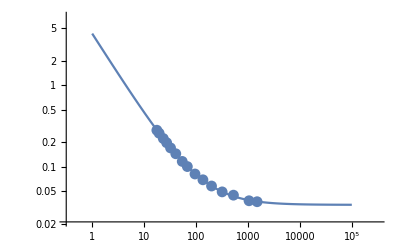

a | 0.592424
b | -4.25143
c | 0.0342709

```mathematica
data=Import["/Users/kazuki/Projects/Atom-work/object-validation/jets/make_yaml/eta_12-21.dat"];
fit=FindFit[data,model,{a0,b0,c0},x];
modelf=Function[{x},Evaluate[model/.fit]];
Fa=LogLogPlot[modelf[x],{x,1,100000},Epilog->Map[Point,data]];
Fb=ListLogLogPlot[data];
Show[Fa,Fb]
{a,b,c}={a0,b0,c0}/.fit;
{{"a",a},{"b",b},{"c",c}}//TableForm
```

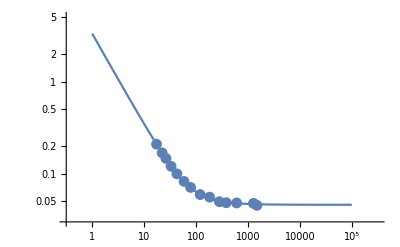

a | 0.284608
b | 3.32814
c | 0.0456649

```mathematica
data=Import["/Users/kazuki/Projects/Atom-work/object-validation/jets/make_yaml/eta_21-28.dat"];
fit=FindFit[data,model,{a0,b0,c0},x];
modelf=Function[{x},Evaluate[model/.fit]];
Fa=LogLogPlot[modelf[x],{x,1,100000},Epilog->Map[Point,data]];
Fb=ListLogLogPlot[data];
Show[Fa,Fb]
{a,b,c}={a0,b0,c0}/.fit;
{{"a",a},{"b",b},{"c",c}}//TableForm
```